# Set - Up

## Trade - Offs

```mathematica
(* Baseline transformed traits (no care)*)
muStar[params_]:=(θ/. params);
rStar[params_]:=(s*Exp[-(1-θ)])/. params;
nuStar[params_]:=(1-(1-ν0)*Exp[-(1-θ)])/. params;
sigmaJStar[params_]:=(1-(1-σJ0)*Exp[-(1-θ)])/. params;

(* Exponential trade-off*)
tradeOff["Exp"][params_,c_]:=Module[{mu0,r0,nu0b,sigmaJ0b},mu0=muStar[params];
r0=rStar[params];
nu0b=nuStar[params];
sigmaJ0b=sigmaJStar[params];
{mu0*Exp[-a*c],r0*Exp[-c],1-(1-nu0b)*Exp[-c],1-(1-sigmaJ0b)*Exp[-a*c]}/. params];

(* Saturating trade-off*)
tradeOff["Saturating"][params_,c_]:=Module[{mu0,r0,nu0b,sigmaJ0b,V=0.9,Khalf=0.3,sigmaJMax=0.9,costR=0.8,costNu=0.8},mu0=muStar[params];
r0=rStar[params];
nu0b=nuStar[params];
sigmaJ0b=sigmaJStar[params];
{mu0*(1-(V*c)/(Khalf+c)),r0*Exp[-costR*c],1-(1-nu0b)*Exp[-costNu*c],sigmaJ0b+(sigmaJMax-sigmaJ0b)*(c/(Khalf+c))}/. params];

(* Sigmoid trade-off*)
tradeOff["Sigmoid"][params_,c_]:=Module[{mu0,r0,nu0b,sigmaJ0b,k=10.,c0=0.3,sigmaJMax=1,L,L0,Lnorm},mu0=muStar[params];
r0=rStar[params];
nu0b=nuStar[params];
sigmaJ0b=sigmaJStar[params];
L[x_]:=1/(1+Exp[-k*(x-c0)]);
L0=L[0];
Lnorm[x_]:=(L[x]-L0)/(1-L0);
{mu0*(1-L[c]),r0*Exp[-c],1-(1-nu0b)*Exp[-c],sigmaJ0b+(sigmaJMax-sigmaJ0b)*Lnorm[c]}/. params];
```

## Optimal parameters

```mathematica
baseParamsMaturation={θ->0.8,ν0->0.1,σJ0->0.323823,s->6.,K->250,a->6};

meanME=0.2;
careVals=Range[0,2,0.02];
```

## Distribution

```mathematica
maturationRateDist[mean_,kappa_]:=Module[{alpha,beta},alpha=mean*kappa;
beta=(1-mean)*kappa;
BetaDistribution[alpha,beta]]
```

## Functions

```mathematica
getFitFixedC[params_,shape_String:"Exp"]:=Module[{μres,rres,νres,σJres,μmut,rmut,νmut,σJmut,A,mat,res,V},
(*resident:no care*)
{μres,rres,νres,σJres}=tradeOff[shape][params,0];
(*mutant:fixed care c=0.5*)
{μmut,rmut,νmut,σJmut}=tradeOff[shape][params,0.5];
(*resident equilibrium*)
A=(K*(1-(((νres/σJres)*(1+(μres/mE)))/rres)))/. params//N;
(*Jacobian*)
mat={{-λ-mE-μmut,rmut*(1-A/K)},{mE*σJmut,-λ-νmut}}/. params;
(*dominant eigenvalue*)
res=NSolve[Det[mat]==0,λ];
V=(λ/. res[[2]])/. params//N//Re;
V]

getFitAtC[params_,c_,shape_String:"Exp"]:=Module[{μres,rres,νres,σJres,μmut,rmut,νmut,σJmut,A,mat,res,V},
(*resident:no care*)
{μres,rres,νres,σJres}=tradeOff[shape][params,0];
(*mutant:care=c*)
{μmut,rmut,νmut,σJmut}=tradeOff[shape][params,c];
(*resident equilibrium*)
A=(K*(1-(((νres/σJres)*(1+(μres/mE)))/rres)))/. params//N;
(*Jacobian*)
mat={{-λ-mE-μmut,rmut*(1-A/K)},{mE*σJmut,-λ-νmut}}/. params;
(*dominant eigenvalue*)
res=NSolve[Det[mat]==0,λ];
V=(λ/. res[[2]])/. params//N//Re;
V]
```

## Big Function

```mathematica
runMaturationRateCase[kappa_,n_,seed_,shape_String:"Exp"]:=Module[
{mEVals,(*sampled maturation rate values*)
paramSets,(*parameter sets with different maturation values*)
fitnessFixedC,(*fitness values at fixed care c=0.5*)
resultsFixedC,(*paired (maturation x fitness) values*)
fitnessByCare,(*fitness values across all care levels*)
meanByCare,(*mean fitness across care*)
sdByCare          (*standard deviation of fitness across care*)},

(*fix seed*)
SeedRandom[seed];

(*draw values*)
mEVals=RandomVariate[maturationRateDist[meanME,kappa],n];

(*plot sampled maturation rate distribution*)Print[Histogram[mEVals,20,AxesLabel->{"Maturation rate (mE)","Frequency"},PlotLabel->"Maturation rate distribution ("<>shape<>", κ = "<>ToString[kappa]<>", n = "<>ToString[n]<>")"]];

(*build parameter sets by replacing maturation rate*)
paramSets=Table[Join[baseParamsMaturation,{mE->me}],{me,mEVals}];

(*invasion fitness at fixed care c=0.5*)
fitnessFixedC=Table[getFitFixedC[paramSets[[i]],shape],{i,Length[paramSets]}];

(*pair maturation value with fitness*)
resultsFixedC=Transpose[{mEVals,fitnessFixedC}];

(*plot fitness vs maturation rate at c=0.5*)Print[ListPlot[resultsFixedC,AxesLabel->{"Maturation rate (mE)","Fitness (λ)"},PlotRange->All,PlotLabel->"Fitness vs maturation rate ("<>shape<>", c = 0.5, κ = "<>ToString[kappa]<>", n = "<>ToString[n]<>")"]];

(*invasion fitness across full care range*)
fitnessByCare=Table[{c,Table[getFitAtC[paramSets[[i]],c,shape],{i,Length[paramSets]}]},{c,careVals}];

(*mean fitness across care*)
meanByCare={#[[1]],Mean[#[[2]]]}&/@fitnessByCare;

(*standard deviation of fitness across care*)
sdByCare={#[[1]],StandardDeviation[#[[2]]]}&/@fitnessByCare;

(*plot mean fitness vs care*)Print[ListPlot[meanByCare,Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotRange->All,PlotLabel->"Mean fitness vs care (mE, "<>shape<>", κ = "<>ToString[kappa]<>", n = "<>ToString[n]<>")"]];

(*plot SD of fitness vs care*)Print[ListPlot[sdByCare,Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotRange->All,PlotLabel->"SD of fitness vs care (mE, "<>shape<>", κ = "<>ToString[kappa]<>", n = "<>ToString[n]<>")"]];

{meanByCare,sdByCare}];
```

# Exponential

## Bulk Code

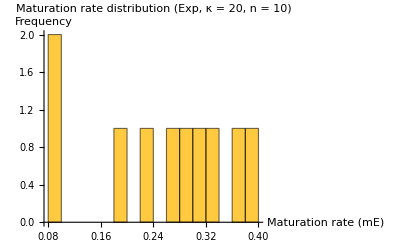

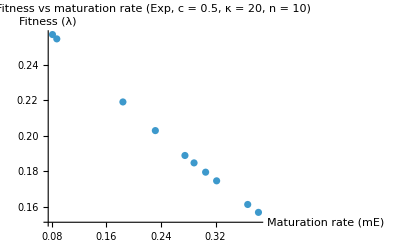

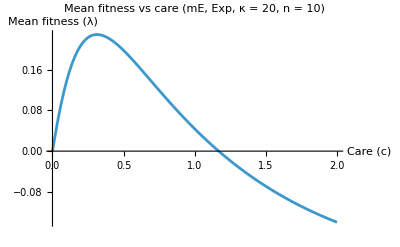

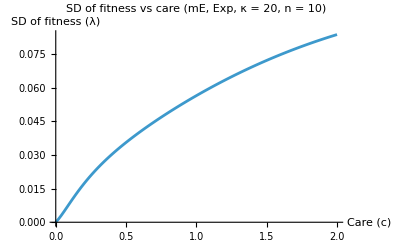

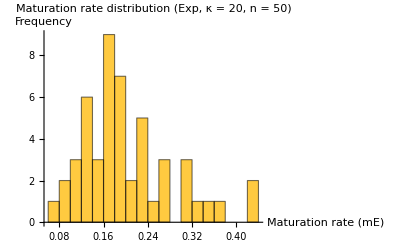

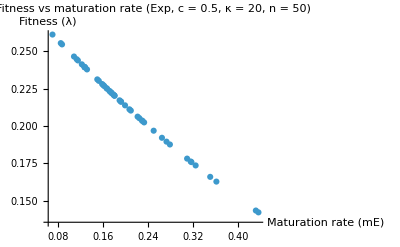

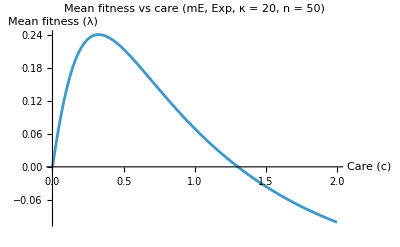

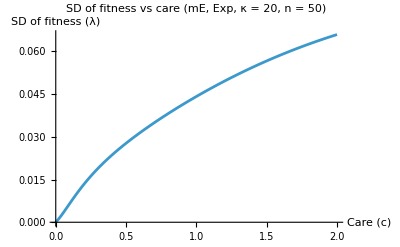

```mathematica
{meanFitnessByCareMEA10Exp,sdFitnessByCareMEA10Exp}=runMaturationRateCase[20,10,2010,"Exp"];

{meanFitnessByCareMEA50Exp,sdFitnessByCareMEA50Exp}=runMaturationRateCase[20,50,2050,"Exp"];

{meanFitnessByCareMEA100Exp,sdFitnessByCareMEA100Exp}=runMaturationRateCase[20,100,2100,"Exp"];



{meanFitnessByCareMEB10Exp,sdFitnessByCareMEB10Exp}=runMaturationRateCase[10,10,1010,"Exp"];

{meanFitnessByCareMEB50Exp,sdFitnessByCareMEB50Exp}=runMaturationRateCase[10,50,1050,"Exp"];

{meanFitnessByCareMEB100Exp,sdFitnessByCareMEB100Exp}=runMaturationRateCase[10,100,1100,"Exp"];



{meanFitnessByCareMEC10Exp,sdFitnessByCareMEC10Exp}=runMaturationRateCase[30,10,3010,"Exp"];

{meanFitnessByCareMEC50Exp,sdFitnessByCareMEC50Exp}=runMaturationRateCase[30,50,3050,"Exp"];

{meanFitnessByCareMEC100Exp,sdFitnessByCareMEC100Exp}=runMaturationRateCase[30,100,3100,"Exp"];
```

## Overlaid Plots

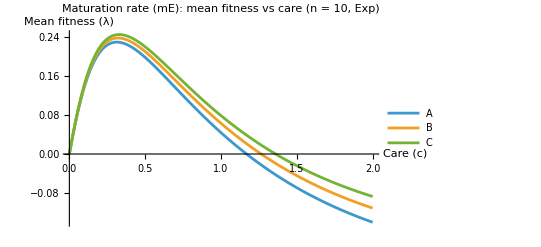

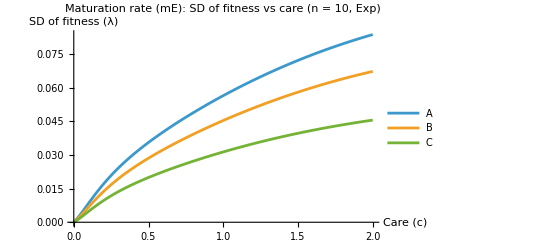

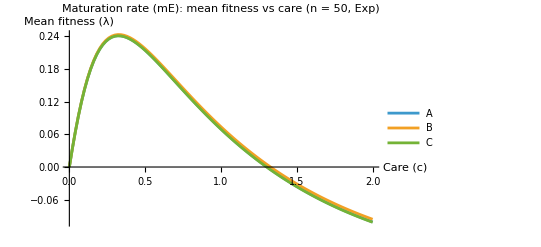

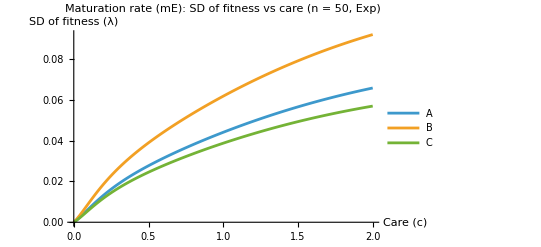

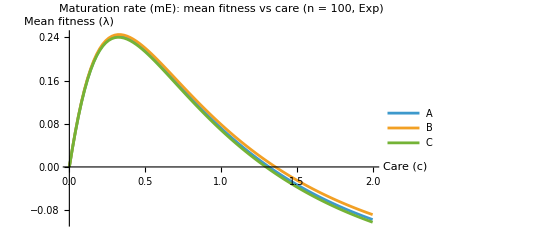

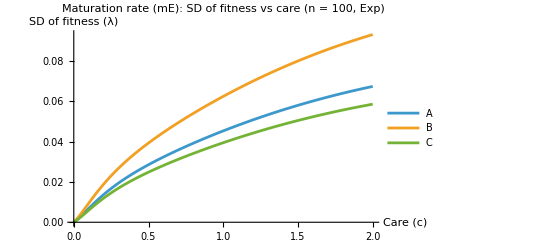

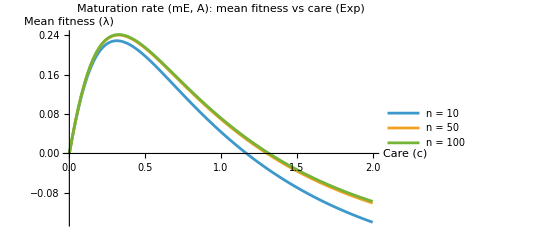

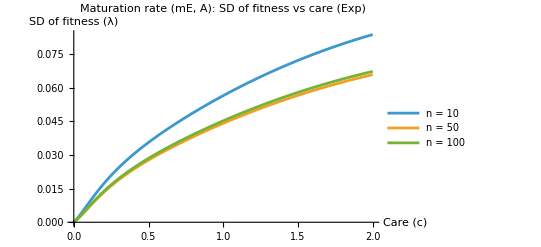

```mathematica
(*Grouped by sample size*)

ListPlot[{meanFitnessByCareMEA10Exp,meanFitnessByCareMEB10Exp,meanFitnessByCareMEC10Exp},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Maturation rate (mE): mean fitness vs care (n = 10, Exp)"]

ListPlot[{sdFitnessByCareMEA10Exp,sdFitnessByCareMEB10Exp,sdFitnessByCareMEC10Exp},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Maturation rate (mE): SD of fitness vs care (n = 10, Exp)"]


ListPlot[{meanFitnessByCareMEA50Exp,meanFitnessByCareMEB50Exp,meanFitnessByCareMEC50Exp},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Maturation rate (mE): mean fitness vs care (n = 50, Exp)"]

ListPlot[{sdFitnessByCareMEA50Exp,sdFitnessByCareMEB50Exp,sdFitnessByCareMEC50Exp},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Maturation rate (mE): SD of fitness vs care (n = 50, Exp)"]


ListPlot[{meanFitnessByCareMEA100Exp,meanFitnessByCareMEB100Exp,meanFitnessByCareMEC100Exp},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Maturation rate (mE): mean fitness vs care (n = 100, Exp)"]

ListPlot[{sdFitnessByCareMEA100Exp,sdFitnessByCareMEB100Exp,sdFitnessByCareMEC100Exp},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Maturation rate (mE): SD of fitness vs care (n = 100, Exp)"]



(*Grouped by distribution*)

ListPlot[{meanFitnessByCareMEA10Exp,meanFitnessByCareMEA50Exp,meanFitnessByCareMEA100Exp},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Maturation rate (mE, A): mean fitness vs care (Exp)"]

ListPlot[{sdFitnessByCareMEA10Exp,sdFitnessByCareMEA50Exp,sdFitnessByCareMEA100Exp},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Maturation rate (mE, A): SD of fitness vs care (Exp)"]


ListPlot[{meanFitnessByCareMEB10Exp,meanFitnessByCareMEB50Exp,meanFitnessByCareMEB100Exp},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Maturation rate (mE, B): mean fitness vs care (Exp)"]

ListPlot[{sdFitnessByCareMEB10Exp,sdFitnessByCareMEB50Exp,sdFitnessByCareMEB100Exp},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Maturation rate (mE, B): SD of fitness vs care (Exp)"]


ListPlot[{meanFitnessByCareMEC10Exp,meanFitnessByCareMEC50Exp,meanFitnessByCareMEC100Exp},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Maturation rate (mE, C): mean fitness vs care (Exp)"]

ListPlot[{sdFitnessByCareMEC10Exp,sdFitnessByCareMEC50Exp,sdFitnessByCareMEC100Exp},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Maturation rate (mE, C): SD of fitness vs care (Exp)"]
```

## Tables

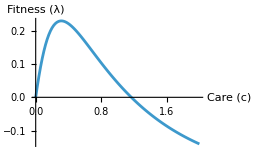
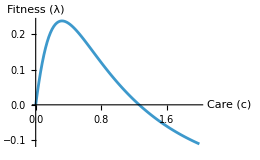
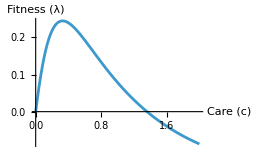
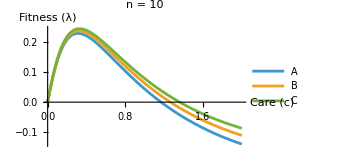
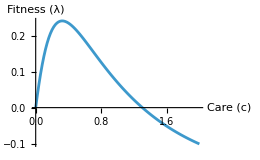
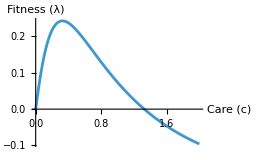
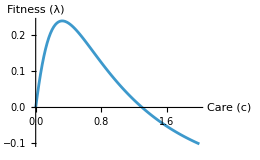
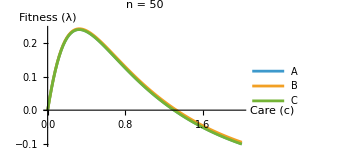
Mean | Distribution A | Distribution B | Distribution C | Compiled
N = 10 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 50 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Compiled | -Graphics- | -Graphics- | -Graphics- | -Graphics-

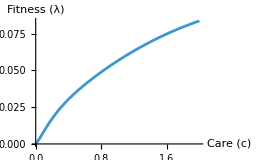
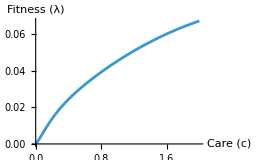
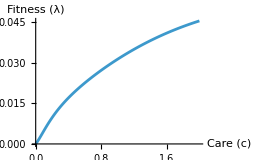
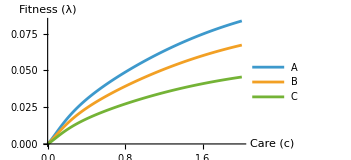
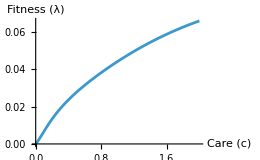
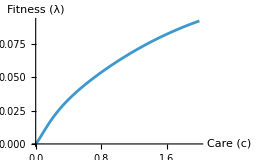
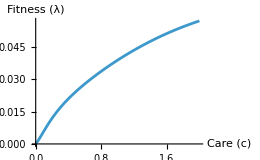
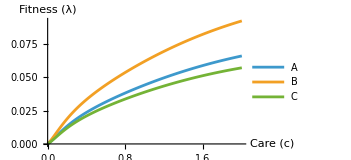
SD | Distribution A | Distribution B | Distribution C | Compiled
N = 10 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 50 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Compiled | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
plotOpts={Joined->True,PlotRange->All,AxesLabel->{"Care (c)","Fitness (λ)"},ImageSize->260};
meanMEA10Exp=ListPlot[{meanFitnessByCareMEA10Exp,meanFitnessByCareMEB10Exp,meanFitnessByCareMEC10Exp},PlotLegends->{"A","B","C"},PlotLabel->"n = 10",plotOpts];

meanMEA50Exp=ListPlot[{meanFitnessByCareMEA50Exp,meanFitnessByCareMEB50Exp,meanFitnessByCareMEC50Exp},PlotLegends->{"A","B","C"},PlotLabel->"n = 50",plotOpts];

meanMEA100Exp=ListPlot[{meanFitnessByCareMEA100Exp,meanFitnessByCareMEB100Exp,meanFitnessByCareMEC100Exp},PlotLegends->{"A","B","C"},PlotLabel->"n = 100",plotOpts];

meanMECompAExp=ListPlot[{meanFitnessByCareMEA10Exp,meanFitnessByCareMEA50Exp,meanFitnessByCareMEA100Exp},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution A",plotOpts];

meanMECompBExp=ListPlot[{meanFitnessByCareMEB10Exp,meanFitnessByCareMEB50Exp,meanFitnessByCareMEB100Exp},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution B",plotOpts];

meanMECompCExp=ListPlot[{meanFitnessByCareMEC10Exp,meanFitnessByCareMEC50Exp,meanFitnessByCareMEC100Exp},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution C",plotOpts];

meanTableMEExp=Grid[{{Style["Mean",16,Bold,Background->LightPink],Style["Distribution A",Bold],Style["Distribution B",Bold],Style["Distribution C",Bold],Style["Compiled",Bold]},{Style["N = 10",Bold],ListPlot[{meanFitnessByCareMEA10Exp},plotOpts],ListPlot[{meanFitnessByCareMEB10Exp},plotOpts],ListPlot[{meanFitnessByCareMEC10Exp},plotOpts],meanMEA10Exp},{Style["N = 50",Bold],ListPlot[{meanFitnessByCareMEA50Exp},plotOpts],ListPlot[{meanFitnessByCareMEB50Exp},plotOpts],ListPlot[{meanFitnessByCareMEC50Exp},plotOpts],meanMEA50Exp},{Style["N = 100",Bold],ListPlot[{meanFitnessByCareMEA100Exp},plotOpts],ListPlot[{meanFitnessByCareMEB100Exp},plotOpts],ListPlot[{meanFitnessByCareMEC100Exp},plotOpts],meanMEA100Exp},{Style["Compiled",Bold],meanMECompAExp,meanMECompBExp,meanMECompCExp,Graphics[{}]}},Frame->All,Spacings->{2,2},Alignment->Center];

sdTableMEExp=Grid[{{Style["SD",16,Bold,Background->LightPink],Style["Distribution A",Bold],Style["Distribution B",Bold],Style["Distribution C",Bold],Style["Compiled",Bold]},{Style["N = 10",Bold],ListPlot[{sdFitnessByCareMEA10Exp},plotOpts],ListPlot[{sdFitnessByCareMEB10Exp},plotOpts],ListPlot[{sdFitnessByCareMEC10Exp},plotOpts],ListPlot[{sdFitnessByCareMEA10Exp,sdFitnessByCareMEB10Exp,sdFitnessByCareMEC10Exp},PlotLegends->{"A","B","C"},plotOpts]},{Style["N = 50",Bold],ListPlot[{sdFitnessByCareMEA50Exp},plotOpts],ListPlot[{sdFitnessByCareMEB50Exp},plotOpts],ListPlot[{sdFitnessByCareMEC50Exp},plotOpts],ListPlot[{sdFitnessByCareMEA50Exp,sdFitnessByCareMEB50Exp,sdFitnessByCareMEC50Exp},PlotLegends->{"A","B","C"},plotOpts]},{Style["N = 100",Bold],ListPlot[{sdFitnessByCareMEA100Exp},plotOpts],ListPlot[{sdFitnessByCareMEB100Exp},plotOpts],ListPlot[{sdFitnessByCareMEC100Exp},plotOpts],ListPlot[{sdFitnessByCareMEA100Exp,sdFitnessByCareMEB100Exp,sdFitnessByCareMEC100Exp},PlotLegends->{"A","B","C"},plotOpts]},{Style["Compiled",Bold],ListPlot[{sdFitnessByCareMEA10Exp,sdFitnessByCareMEA50Exp,sdFitnessByCareMEA100Exp},PlotLegends->{"n = 10","n = 50","n = 100"},plotOpts],ListPlot[{sdFitnessByCareMEB10Exp,sdFitnessByCareMEB50Exp,sdFitnessByCareMEB100Exp},PlotLegends->{"n = 10","n = 50","n = 100"},plotOpts],ListPlot[{sdFitnessByCareMEC10Exp,sdFitnessByCareMEC50Exp,sdFitnessByCareMEC100Exp},PlotLegends->{"n = 10","n = 50","n = 100"},plotOpts],Graphics[{}]}},Frame->All,Spacings->{2,2},Alignment->Center];

meanTableMEExp
sdTableMEExp
```

## Mean Plots

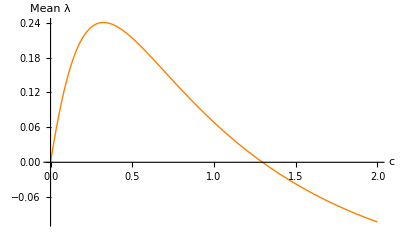

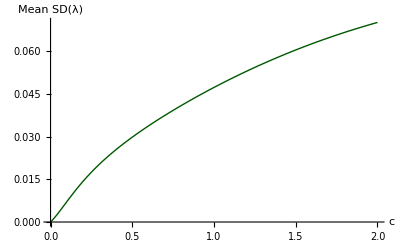

```mathematica
allMeanCurvesExp={meanFitnessByCareMEA10Exp,meanFitnessByCareMEA50Exp,meanFitnessByCareMEA100Exp,meanFitnessByCareMEB10Exp,meanFitnessByCareMEB50Exp,meanFitnessByCareMEB100Exp,meanFitnessByCareMEC10Exp,meanFitnessByCareMEC50Exp,meanFitnessByCareMEC100Exp};

allSDCurvesExp={sdFitnessByCareMEA10Exp,sdFitnessByCareMEA50Exp,sdFitnessByCareMEA100Exp,sdFitnessByCareMEB10Exp,sdFitnessByCareMEB50Exp,sdFitnessByCareMEB100Exp,sdFitnessByCareMEC10Exp,sdFitnessByCareMEC50Exp,sdFitnessByCareMEC100Exp};

careValues=allMeanCurvesExp[[1]][[All,1]];

overallMeanExp=Transpose[{careValues,Mean/@Transpose[allMeanCurvesExp[[All,All,2]]]}];

overallSDExp=Transpose[{careValues,Mean/@Transpose[allSDCurvesExp[[All,All,2]]]}];

plotOverallMeanExp=ListPlot[overallMeanExp,Joined->True,PlotRange->All,PlotStyle->Directive[Orange,Thick],AxesLabel->{"c","Mean λ"}];

plotOverallSDExp=ListPlot[overallSDExp,Joined->True,PlotRange->All,PlotStyle->Directive[RGBColor[0,0.35,0],Thick],AxesLabel->{"c","Mean SD(λ)"}];

plotOverallMeanExp
plotOverallSDExp
```

# Saturating

## Bulk Code

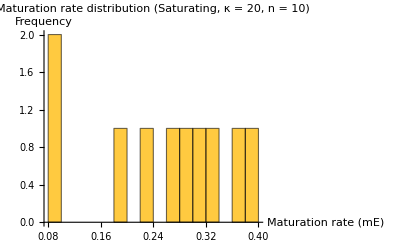

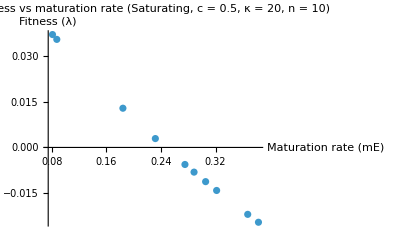

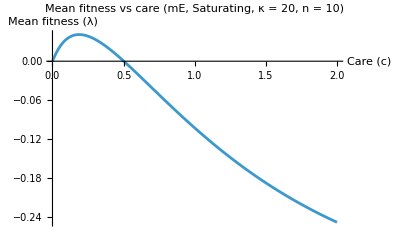

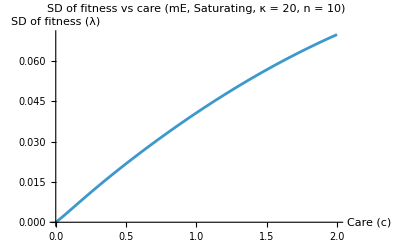

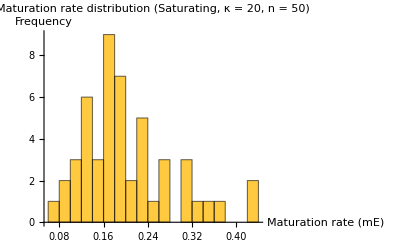

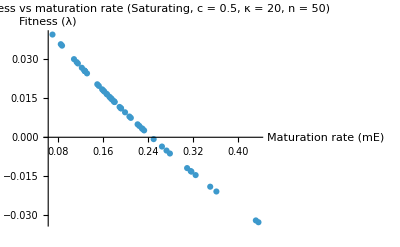

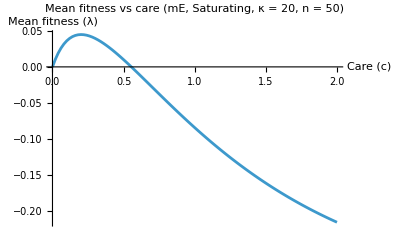

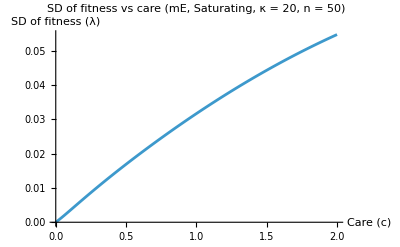

```mathematica
{meanFitnessByCareMEA10Sat,sdFitnessByCareMEA10Sat}=runMaturationRateCase[20,10,2010,"Saturating"];

{meanFitnessByCareMEA50Sat,sdFitnessByCareMEA50Sat}=runMaturationRateCase[20,50,2050,"Saturating"];

{meanFitnessByCareMEA100Sat,sdFitnessByCareMEA100Sat}=runMaturationRateCase[20,100,2100,"Saturating"];



{meanFitnessByCareMEB10Sat,sdFitnessByCareMEB10Sat}=runMaturationRateCase[10,10,1010,"Saturating"];

{meanFitnessByCareMEB50Sat,sdFitnessByCareMEB50Sat}=runMaturationRateCase[10,50,1050,"Saturating"];

{meanFitnessByCareMEB100Sat,sdFitnessByCareMEB100Sat}=runMaturationRateCase[10,100,1100,"Saturating"];



{meanFitnessByCareMEC10Sat,sdFitnessByCareMEC10Sat}=runMaturationRateCase[30,10,3010,"Saturating"];

{meanFitnessByCareMEC50Sat,sdFitnessByCareMEC50Sat}=runMaturationRateCase[30,50,3050,"Saturating"];

{meanFitnessByCareMEC100Sat,sdFitnessByCareMEC100Sat}=runMaturationRateCase[30,100,3100,"Saturating"];
```

## Diagnostic Plots

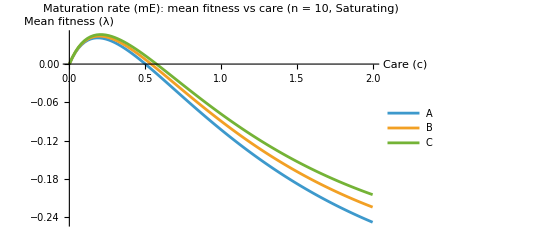

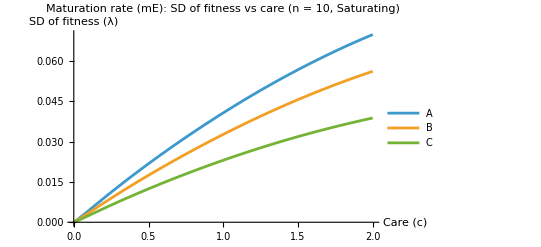

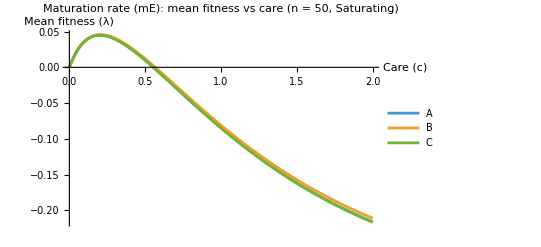

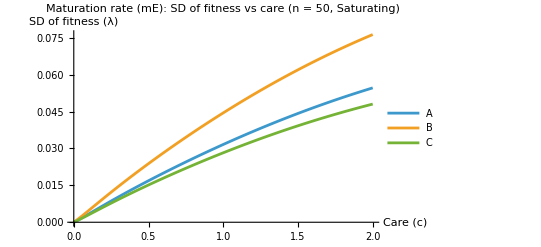

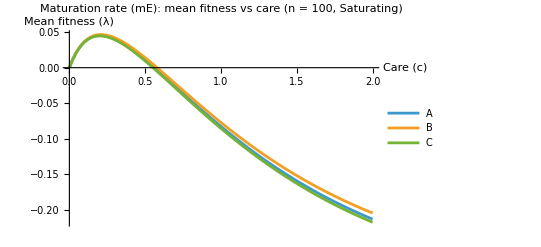

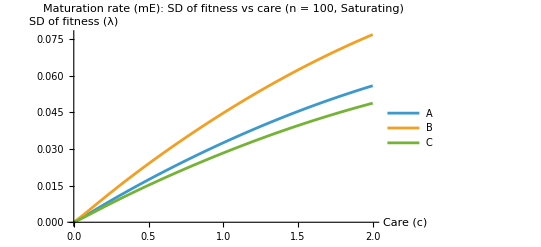

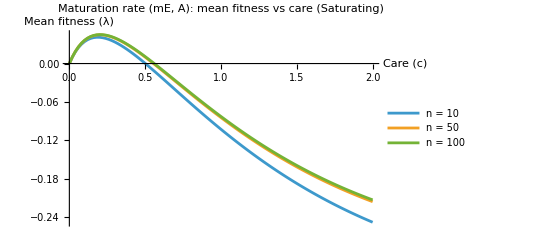

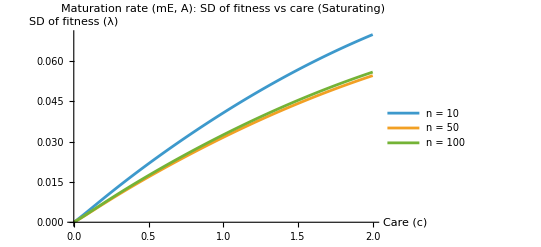

```mathematica
(*grouped by sample size*)

ListPlot[{meanFitnessByCareMEA10Sat,meanFitnessByCareMEB10Sat,meanFitnessByCareMEC10Sat},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"A","B","C"},PlotLabel->"Maturation rate (mE): mean fitness vs care (n = 10, Saturating)"]

ListPlot[{sdFitnessByCareMEA10Sat,sdFitnessByCareMEB10Sat,sdFitnessByCareMEC10Sat},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"A","B","C"},PlotLabel->"Maturation rate (mE): SD of fitness vs care (n = 10, Saturating)"]


ListPlot[{meanFitnessByCareMEA50Sat,meanFitnessByCareMEB50Sat,meanFitnessByCareMEC50Sat},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"A","B","C"},PlotLabel->"Maturation rate (mE): mean fitness vs care (n = 50, Saturating)"]

ListPlot[{sdFitnessByCareMEA50Sat,sdFitnessByCareMEB50Sat,sdFitnessByCareMEC50Sat},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"A","B","C"},PlotLabel->"Maturation rate (mE): SD of fitness vs care (n = 50, Saturating)"]


ListPlot[{meanFitnessByCareMEA100Sat,meanFitnessByCareMEB100Sat,meanFitnessByCareMEC100Sat},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"A","B","C"},PlotLabel->"Maturation rate (mE): mean fitness vs care (n = 100, Saturating)"]

ListPlot[{sdFitnessByCareMEA100Sat,sdFitnessByCareMEB100Sat,sdFitnessByCareMEC100Sat},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"A","B","C"},PlotLabel->"Maturation rate (mE): SD of fitness vs care (n = 100, Saturating)"]


(*grouped by distribution*)

ListPlot[{meanFitnessByCareMEA10Sat,meanFitnessByCareMEA50Sat,meanFitnessByCareMEA100Sat},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Maturation rate (mE, A): mean fitness vs care (Saturating)"]

ListPlot[{sdFitnessByCareMEA10Sat,sdFitnessByCareMEA50Sat,sdFitnessByCareMEA100Sat},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Maturation rate (mE, A): SD of fitness vs care (Saturating)"]


ListPlot[{meanFitnessByCareMEB10Sat,meanFitnessByCareMEB50Sat,meanFitnessByCareMEB100Sat},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Maturation rate (mE, B): mean fitness vs care (Saturating)"]

ListPlot[{sdFitnessByCareMEB10Sat,sdFitnessByCareMEB50Sat,sdFitnessByCareMEB100Sat},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Maturation rate (mE, B): SD of fitness vs care (Saturating)"]


ListPlot[{meanFitnessByCareMEC10Sat,meanFitnessByCareMEC50Sat,meanFitnessByCareMEC100Sat},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Maturation rate (mE, C): mean fitness vs care (Saturating)"]

ListPlot[{sdFitnessByCareMEC10Sat,sdFitnessByCareMEC50Sat,sdFitnessByCareMEC100Sat},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Maturation rate (mE, C): SD of fitness vs care (Saturating)"]
```

## Tables

```mathematica
meanMEA10Sat=ListPlot[{meanFitnessByCareMEA10Sat,meanFitnessByCareMEB10Sat,meanFitnessByCareMEC10Sat},PlotLegends->{"A","B","C"},PlotLabel->"n = 10",plotOpts];

meanMEA50Sat=ListPlot[{meanFitnessByCareMEA50Sat,meanFitnessByCareMEB50Sat,meanFitnessByCareMEC50Sat},PlotLegends->{"A","B","C"},PlotLabel->"n = 50",plotOpts];

meanMEA100Sat=ListPlot[{meanFitnessByCareMEA100Sat,meanFitnessByCareMEB100Sat,meanFitnessByCareMEC100Sat},PlotLegends->{"A","B","C"},PlotLabel->"n = 100",plotOpts];

meanMECompASat=ListPlot[{meanFitnessByCareMEA10Sat,meanFitnessByCareMEA50Sat,meanFitnessByCareMEA100Sat},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution A",plotOpts];

meanMECompBSat=ListPlot[{meanFitnessByCareMEB10Sat,meanFitnessByCareMEB50Sat,meanFitnessByCareMEB100Sat},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution B",plotOpts];

meanMECompCSat=ListPlot[{meanFitnessByCareMEC10Sat,meanFitnessByCareMEC50Sat,meanFitnessByCareMEC100Sat},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution C",plotOpts];

meanTableMESat=Grid[{{Style["Mean",16,Bold,Background->LightPink],Style["Distribution A",Bold],Style["Distribution B",Bold],Style["Distribution C",Bold],Style["Compiled",Bold]},{Style["N = 10",Bold],ListPlot[{meanFitnessByCareMEA10Sat},plotOpts],ListPlot[{meanFitnessByCareMEB10Sat},plotOpts],ListPlot[{meanFitnessByCareMEC10Sat},plotOpts],meanMEA10Sat},{Style["N = 50",Bold],ListPlot[{meanFitnessByCareMEA50Sat},plotOpts],ListPlot[{meanFitnessByCareMEB50Sat},plotOpts],ListPlot[{meanFitnessByCareMEC50Sat},plotOpts],meanMEA50Sat},{Style["N = 100",Bold],ListPlot[{meanFitnessByCareMEA100Sat},plotOpts],ListPlot[{meanFitnessByCareMEB100Sat},plotOpts],ListPlot[{meanFitnessByCareMEC100Sat},plotOpts],meanMEA100Sat},{Style["Compiled",Bold],meanMECompASat,meanMECompBSat,meanMECompCSat,Graphics[{}]}},Frame->All,Spacings->{2,2},Alignment->Center];

sdTableMESat=Grid[{{Style["SD",16,Bold,Background->LightPink],Style["Distribution A",Bold],Style["Distribution B",Bold],Style["Distribution C",Bold],Style["Compiled",Bold]},{Style["N = 10",Bold],ListPlot[{sdFitnessByCareMEA10Sat},plotOpts],ListPlot[{sdFitnessByCareMEB10Sat},plotOpts],ListPlot[{sdFitnessByCareMEC10Sat},plotOpts],ListPlot[{sdFitnessByCareMEA10Sat,sdFitnessByCareMEB10Sat,sdFitnessByCareMEC10Sat},PlotLegends->{"A","B","C"},plotOpts]},{Style["N = 50",Bold],ListPlot[{sdFitnessByCareMEA50Sat},plotOpts],ListPlot[{sdFitnessByCareMEB50Sat},plotOpts],ListPlot[{sdFitnessByCareMEC50Sat},plotOpts],ListPlot[{sdFitnessByCareMEA50Sat,sdFitnessByCareMEB50Sat,sdFitnessByCareMEC50Sat},PlotLegends->{"A","B","C"},plotOpts]},{Style["N = 100",Bold],ListPlot[{sdFitnessByCareMEA100Sat},plotOpts],ListPlot[{sdFitnessByCareMEB100Sat},plotOpts],ListPlot[{sdFitnessByCareMEC100Sat},plotOpts],ListPlot[{sdFitnessByCareMEA100Sat,sdFitnessByCareMEB100Sat,sdFitnessByCareMEC100Sat},PlotLegends->{"A","B","C"},plotOpts]},{Style["Compiled",Bold],ListPlot[{sdFitnessByCareMEA10Sat,sdFitnessByCareMEA50Sat,sdFitnessByCareMEA100Sat},PlotLegends->{"n = 10","n = 50","n = 100"},plotOpts],ListPlot[{sdFitnessByCareMEB10Sat,sdFitnessByCareMEB50Sat,sdFitnessByCareMEB100Sat},PlotLegends->{"n = 10","n = 50","n = 100"},plotOpts],ListPlot[{sdFitnessByCareMEC10Sat,sdFitnessByCareMEC50Sat,sdFitnessByCareMEC100Sat},PlotLegends->{"n = 10","n = 50","n = 100"},plotOpts],Graphics[{}]}},Frame->All,Spacings->{2,2},Alignment->Center];

meanTableMESat
sdTableMESat
```

Mean | Distribution A | Distribution B | Distribution C | Compiled
N = 10 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 50 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Compiled | -Graphics- | -Graphics- | -Graphics- | -Graphics-

SD | Distribution A | Distribution B | Distribution C | Compiled
N = 10 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 50 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Compiled | -Graphics- | -Graphics- | -Graphics- | -Graphics-

## Mean Plots

```mathematica
allMeanCurvesSat={meanFitnessByCareMEA10Sat,meanFitnessByCareMEA50Sat,meanFitnessByCareMEA100Sat,meanFitnessByCareMEB10Sat,meanFitnessByCareMEB50Sat,meanFitnessByCareMEB100Sat,meanFitnessByCareMEC10Sat,meanFitnessByCareMEC50Sat,meanFitnessByCareMEC100Sat};


allSDCurvesSat={sdFitnessByCareMEA10Sat,sdFitnessByCareMEA50Sat,sdFitnessByCareMEA100Sat,sdFitnessByCareMEB10Sat,sdFitnessByCareMEB50Sat,sdFitnessByCareMEB100Sat,sdFitnessByCareMEC10Sat,sdFitnessByCareMEC50Sat,sdFitnessByCareMEC100Sat};

careValuesSat=allMeanCurvesSat[[1]][[All,1]];

overallMeanSat=Transpose[{careValuesSat,Mean/@Transpose[allMeanCurvesSat[[All,All,2]]]}];

overallSDSat=Transpose[{careValuesSat,Mean/@Transpose[allSDCurvesSat[[All,All,2]]]}];

plotOverallMeanSat=ListPlot[overallMeanSat,Joined->True,PlotRange->All,PlotStyle->Directive[Orange,Thick],AxesLabel->{"c","Mean λ"}];

plotOverallSDSat=ListPlot[overallSDSat,Joined->True,PlotRange->All,PlotStyle->Directive[RGBColor[0,0.35,0],Thick],AxesLabel->{"c","Mean SD(λ)"}];

plotOverallMeanSat
plotOverallSDSat
```

-Graphics-

-Graphics-

# Sigmoid

## Bulk Code

```mathematica
{meanFitnessByCareMEA10Sig,sdFitnessByCareMEA10Sig}=runMaturationRateCase[20,10,2010,"Sigmoid"];

{meanFitnessByCareMEA50Sig,sdFitnessByCareMEA50Sig}=runMaturationRateCase[20,50,2050,"Sigmoid"];

{meanFitnessByCareMEA100Sig,sdFitnessByCareMEA100Sig}=runMaturationRateCase[20,100,2100,"Sigmoid"];



{meanFitnessByCareMEB10Sig,sdFitnessByCareMEB10Sig}=runMaturationRateCase[10,10,1010,"Sigmoid"];

{meanFitnessByCareMEB50Sig,sdFitnessByCareMEB50Sig}=runMaturationRateCase[10,50,1050,"Sigmoid"];

{meanFitnessByCareMEB100Sig,sdFitnessByCareMEB100Sig}=runMaturationRateCase[10,100,1100,"Sigmoid"];



{meanFitnessByCareMEC10Sig,sdFitnessByCareMEC10Sig}=runMaturationRateCase[30,10,3010,"Sigmoid"];

{meanFitnessByCareMEC50Sig,sdFitnessByCareMEC50Sig}=runMaturationRateCase[30,50,3050,"Sigmoid"];

{meanFitnessByCareMEC100Sig,sdFitnessByCareMEC100Sig}=runMaturationRateCase[30,100,3100,"Sigmoid"];
```

-Graphics-

-Graphics-

-Graphics-

«33 more identical outputs»

## Diagnostic Plots

```mathematica
(*grouped by sample size*)

ListPlot[{meanFitnessByCareMEA10Sig,meanFitnessByCareMEB10Sig,meanFitnessByCareMEC10Sig},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"A","B","C"},PlotLabel->"Maturation rate (mE): mean fitness vs care (n = 10, Sigmoid)"]

ListPlot[{sdFitnessByCareMEA10Sig,sdFitnessByCareMEB10Sig,sdFitnessByCareMEC10Sig},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"A","B","C"},PlotLabel->"Maturation rate (mE): SD of fitness vs care (n = 10, Sigmoid)"]


ListPlot[{meanFitnessByCareMEA50Sig,meanFitnessByCareMEB50Sig,meanFitnessByCareMEC50Sig},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"A","B","C"},PlotLabel->"Maturation rate (mE): mean fitness vs care (n = 50, Sigmoid)"]

ListPlot[{sdFitnessByCareMEA50Sig,sdFitnessByCareMEB50Sig,sdFitnessByCareMEC50Sig},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"A","B","C"},PlotLabel->"Maturation rate (mE): SD of fitness vs care (n = 50, Sigmoid)"]


ListPlot[{meanFitnessByCareMEA100Sig,meanFitnessByCareMEB100Sig,meanFitnessByCareMEC100Sig},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"A","B","C"},PlotLabel->"Maturation rate (mE): mean fitness vs care (n = 100, Sigmoid)"]

ListPlot[{sdFitnessByCareMEA100Sig,sdFitnessByCareMEB100Sig,sdFitnessByCareMEC100Sig},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"A","B","C"},PlotLabel->"Maturation rate (mE): SD of fitness vs care (n = 100, Sigmoid)"]


(*grouped by distribution*)

ListPlot[{meanFitnessByCareMEA10Sig,meanFitnessByCareMEA50Sig,meanFitnessByCareMEA100Sig},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Maturation rate (mE, A): mean fitness vs care (Sigmoid)"]

ListPlot[{sdFitnessByCareMEA10Sig,sdFitnessByCareMEA50Sig,sdFitnessByCareMEA100Sig},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Maturation rate (mE, A): SD of fitness vs care (Sigmoid)"]


ListPlot[{meanFitnessByCareMEB10Sig,meanFitnessByCareMEB50Sig,meanFitnessByCareMEB100Sig},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Maturation rate (mE, B): mean fitness vs care (Sigmoid)"]

ListPlot[{sdFitnessByCareMEB10Sig,sdFitnessByCareMEB50Sig,sdFitnessByCareMEB100Sig},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Maturation rate (mE, B): SD of fitness vs care (Sigmoid)"]


ListPlot[{meanFitnessByCareMEC10Sig,meanFitnessByCareMEC50Sig,meanFitnessByCareMEC100Sig},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Maturation rate (mE, C): mean fitness vs care (Sigmoid)"]

ListPlot[{sdFitnessByCareMEC10Sig,sdFitnessByCareMEC50Sig,sdFitnessByCareMEC100Sig},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Maturation rate (mE, C): SD of fitness vs care (Sigmoid)"]
```

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

## Tables

```mathematica
meanMEA10Sig=ListPlot[{meanFitnessByCareMEA10Sig,meanFitnessByCareMEB10Sig,meanFitnessByCareMEC10Sig},PlotLegends->{"A","B","C"},PlotLabel->"n = 10",plotOpts];

meanMEA50Sig=ListPlot[{meanFitnessByCareMEA50Sig,meanFitnessByCareMEB50Sig,meanFitnessByCareMEC50Sig},PlotLegends->{"A","B","C"},PlotLabel->"n = 50",plotOpts];

meanMEA100Sig=ListPlot[{meanFitnessByCareMEA100Sig,meanFitnessByCareMEB100Sig,meanFitnessByCareMEC100Sig},PlotLegends->{"A","B","C"},PlotLabel->"n = 100",plotOpts];

meanMECompASig=ListPlot[{meanFitnessByCareMEA10Sig,meanFitnessByCareMEA50Sig,meanFitnessByCareMEA100Sig},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution A",plotOpts];

meanMECompBSig=ListPlot[{meanFitnessByCareMEB10Sig,meanFitnessByCareMEB50Sig,meanFitnessByCareMEB100Sig},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution B",plotOpts];

meanMECompCSig=ListPlot[{meanFitnessByCareMEC10Sig,meanFitnessByCareMEC50Sig,meanFitnessByCareMEC100Sig},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution C",plotOpts];

meanTableMESig=Grid[{{Style["Mean",16,Bold,Background->LightPink],Style["Distribution A",Bold],Style["Distribution B",Bold],Style["Distribution C",Bold],Style["Compiled",Bold]},{Style["N = 10",Bold],ListPlot[{meanFitnessByCareMEA10Sig},plotOpts],ListPlot[{meanFitnessByCareMEB10Sig},plotOpts],ListPlot[{meanFitnessByCareMEC10Sig},plotOpts],meanMEA10Sig},{Style["N = 50",Bold],ListPlot[{meanFitnessByCareMEA50Sig},plotOpts],ListPlot[{meanFitnessByCareMEB50Sig},plotOpts],ListPlot[{meanFitnessByCareMEC50Sig},plotOpts],meanMEA50Sig},{Style["N = 100",Bold],ListPlot[{meanFitnessByCareMEA100Sig},plotOpts],ListPlot[{meanFitnessByCareMEB100Sig},plotOpts],ListPlot[{meanFitnessByCareMEC100Sig},plotOpts],meanMEA100Sig},{Style["Compiled",Bold],meanMECompASig,meanMECompBSig,meanMECompCSig,Graphics[{}]}},Frame->All,Spacings->{2,2},Alignment->Center];

sdTableMESig=Grid[{{Style["SD",16,Bold,Background->LightPink],Style["Distribution A",Bold],Style["Distribution B",Bold],Style["Distribution C",Bold],Style["Compiled",Bold]},{Style["N = 10",Bold],ListPlot[{sdFitnessByCareMEA10Sig},plotOpts],ListPlot[{sdFitnessByCareMEB10Sig},plotOpts],ListPlot[{sdFitnessByCareMEC10Sig},plotOpts],ListPlot[{sdFitnessByCareMEA10Sig,sdFitnessByCareMEB10Sig,sdFitnessByCareMEC10Sig},PlotLegends->{"A","B","C"},plotOpts]},{Style["N = 50",Bold],ListPlot[{sdFitnessByCareMEA50Sig},plotOpts],ListPlot[{sdFitnessByCareMEB50Sig},plotOpts],ListPlot[{sdFitnessByCareMEC50Sig},plotOpts],ListPlot[{sdFitnessByCareMEA50Sig,sdFitnessByCareMEB50Sig,sdFitnessByCareMEC50Sig},PlotLegends->{"A","B","C"},plotOpts]},{Style["N = 100",Bold],ListPlot[{sdFitnessByCareMEA100Sig},plotOpts],ListPlot[{sdFitnessByCareMEB100Sig},plotOpts],ListPlot[{sdFitnessByCareMEC100Sig},plotOpts],ListPlot[{sdFitnessByCareMEA100Sig,sdFitnessByCareMEB100Sig,sdFitnessByCareMEC100Sig},PlotLegends->{"A","B","C"},plotOpts]},{Style["Compiled",Bold],ListPlot[{sdFitnessByCareMEA10Sig,sdFitnessByCareMEA50Sig,sdFitnessByCareMEA100Sig},PlotLegends->{"n = 10","n = 50","n = 100"},plotOpts],ListPlot[{sdFitnessByCareMEB10Sig,sdFitnessByCareMEB50Sig,sdFitnessByCareMEB100Sig},PlotLegends->{"n = 10","n = 50","n = 100"},plotOpts],ListPlot[{sdFitnessByCareMEC10Sig,sdFitnessByCareMEC50Sig,sdFitnessByCareMEC100Sig},PlotLegends->{"n = 10","n = 50","n = 100"},plotOpts],Graphics[{}]}},Frame->All,Spacings->{2,2},Alignment->Center];

meanTableMESig
sdTableMESig
```

Mean | Distribution A | Distribution B | Distribution C | Compiled
N = 10 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 50 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Compiled | -Graphics- | -Graphics- | -Graphics- | -Graphics-

SD | Distribution A | Distribution B | Distribution C | Compiled
N = 10 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 50 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Compiled | -Graphics- | -Graphics- | -Graphics- | -Graphics-

## Mean Plots

```mathematica
allMeanCurvesSig={meanFitnessByCareMEA10Sig,meanFitnessByCareMEA50Sig,meanFitnessByCareMEA100Sig,meanFitnessByCareMEB10Sig,meanFitnessByCareMEB50Sig,meanFitnessByCareMEB100Sig,meanFitnessByCareMEC10Sig,meanFitnessByCareMEC50Sig,meanFitnessByCareMEC100Sig};


allSDCurvesSig={sdFitnessByCareMEA10Sig,sdFitnessByCareMEA50Sig,sdFitnessByCareMEA100Sig,sdFitnessByCareMEB10Sig,sdFitnessByCareMEB50Sig,sdFitnessByCareMEB100Sig,sdFitnessByCareMEC10Sig,sdFitnessByCareMEC50Sig,sdFitnessByCareMEC100Sig};

careValuesSig=allMeanCurvesSig[[1]][[All,1]];

overallMeanSig=Transpose[{careValuesSig,Mean/@Transpose[allMeanCurvesSig[[All,All,2]]]}];

overallSDSig=Transpose[{careValuesSig,Mean/@Transpose[allSDCurvesSig[[All,All,2]]]}];

plotOverallMeanSig=ListPlot[overallMeanSig,Joined->True,PlotRange->All,PlotStyle->Directive[Orange,Thick],AxesLabel->{"c","Mean λ"}];

plotOverallSDSig=ListPlot[overallSDSig,Joined->True,PlotRange->All,PlotStyle->Directive[RGBColor[0,0.35,0],Thick],AxesLabel->{"c","Mean SD(λ)"}];

plotOverallMeanSig
plotOverallSDSig
```

-Graphics-

-Graphics-

# Deterministic Shape

```mathematica
Aexpr[th_,v0_,sj_,ss_,me_,Kval_:250]:=Kval*(1-(((v0/sj)*(1+(th/me)))/ss));


(*Care mutant invading no-care resident*)
getFit[params_,shape_String:"Exp"]:=Module[
{μres,rres,νres,σJres,μmut,rmut,νmut,σJmut,A,mat,res,V},
{μres,rres,νres,σJres}=tradeOff[shape][params,0];
{μmut,rmut,νmut,σJmut}=tradeOff[shape][params,c];
A=(K*(1-(((νres/σJres)*(1+(μres/mE)))/rres)))/. params//N;
mat={{-λ-mE-μmut,rmut*(1-A/K)},{mE*σJmut,-λ-νmut}}/. params;
res=NSolve[Det[mat]==0,λ];
V=(λ/. res[[2]])/. params//Simplify;
Table[{val,Re[N[V/. c->val]]},{val,0,2,0.01}]];

params1={θ->0.8,ν0->0.1,σJ0->0.32383733876731385,s->6,mE->0.2,K->250,a->6};
params2={θ->0.7999967491603689,ν0->0.10000440803427434,σJ0->0.32383733876731385,s->5.999984154933559,mE->0.19999923208705223,K->250,a->6};
params3={θ->0.8,ν0->0.1,σJ0->0.32383733876731385,s->6,mE->0.2,K->250,a->6};

fit1=getFit[params1,"Exp"];
fit2=getFit[params2,"Saturating"];
fit3=getFit[params3,"Sigmoid"];

plotExp=ListPlot[fit1,Joined->True,PlotRange->All,AxesLabel->{"c","λ"}];
plotSaturating=ListPlot[fit2,Joined->True,PlotRange->All,AxesLabel->{"c","λ"}];
plotSigmoid=ListPlot[fit3,Joined->True,PlotRange->All,AxesLabel->{"c","λ"}];

plotExp
plotSaturating
plotSigmoid
```

-Graphics-

-Graphics-

-Graphics-

# SD Trends

```mathematica
imgW=520;
imgH=300;

meanStyleDashedME=Directive[Orange,Thick,Dashed,Opacity[0.45]];
sdStyleDarkME=Directive[RGBColor[0,0.35,0],Thick];

extractXYME[g_]:=Module[{d},d=Cases[Normal[g],Line[pts_]:>pts,Infinity];
First[d]];

makeMeanSDOverlayDashedME[meanG_,sdG_,title_,panelLabel_]:=Module[{meanData,sdData,xMin,xMax,meanMin,meanMax,sdMin,sdMax,meanPad,sdPad,meanPR,sdPR,scale,meanPlot,sdScaledPlot,sdTickVals,sdTickPos,sdTicksRight},meanData=extractXYME[meanG];
sdData=extractXYME[sdG];
xMin=Min[meanData[[All,1]]];
xMax=Max[meanData[[All,1]]];
meanMin=Min[meanData[[All,2]]];
meanMax=Max[meanData[[All,2]]];
sdMin=Min[sdData[[All,2]]];
sdMax=Max[sdData[[All,2]]];
meanPad=0.05*(meanMax-meanMin);
If[meanPad==0,meanPad=0.1];
sdPad=0.05*(sdMax-sdMin);
If[sdPad==0,sdPad=0.1];
meanPR={meanMin-meanPad,meanMax+meanPad};
sdPR={0,sdMax+sdPad};
scale[y_]:=Rescale[y,sdPR,meanPR];
meanPlot=ListPlot[meanData,Joined->True,PlotStyle->meanStyleDashedME,PlotRange->{{xMin,xMax},meanPR}];
sdScaledPlot=ListPlot[({#[[1]],scale[#[[2]]]}&/@sdData),Joined->True,PlotStyle->sdStyleDarkME,PlotRange->{{xMin,xMax},meanPR}];
sdTickVals=N@Subdivide[sdPR[[1]],sdPR[[2]],5];
sdTickPos=scale/@sdTickVals;
sdTicksRight=MapThread[{#1,NumberForm[#2,{Infinity,3}]}&,{sdTickPos,sdTickVals}];
Show[meanPlot,sdScaledPlot,ImageSize->{imgW,imgH},Frame->True,Axes->False,FrameLabel->{{"Mean λ","SD(λ)"},{"c",None}},FrameTicks->{{Automatic,sdTicksRight},{Automatic,None}},PlotLabel->Style[title,16,Bold,Underlined],Epilog->{Inset[Style["("<>panelLabel<>")",14,Bold],Scaled[{0.5,0.95}]]}]];


maturationExpMeanSDDashed=makeMeanSDOverlayDashedME[plotOverallMeanExp,plotOverallSDExp,"Exponential","a"];

maturationSatMeanSDDashed=makeMeanSDOverlayDashedME[plotOverallMeanSat,plotOverallSDSat,"Saturating","b"];

maturationSigMeanSDDashed=makeMeanSDOverlayDashedME[plotOverallMeanSig,plotOverallSDSig,"Sigmoid","c"];

figureLegendDashedME=LineLegend[{meanStyleDashedME,sdStyleDarkME},{"Mean λ","SD(λ)"},LegendLayout->"Row"];

maturationRateMeanSDFigureDashedSideBySide=GraphicsGrid[{{figureLegendDashedME,SpanFromLeft,SpanFromLeft},{maturationExpMeanSDDashed,maturationSatMeanSDDashed,maturationSigMeanSDDashed}},Spacings->{2,1.5},Alignment->Center];

maturationRateMeanSDFigureDashedSideBySide
```

-Graphics-

```mathematica
expMeanData=extractXYME[plotOverallMeanExp];
expSDData=extractXYME[plotOverallSDExp];

(*Get max eigenvalue and care level at max eigenvalue*)
expMaxPoint=First@MaximalBy[expMeanData,Last];
cStarExp=expMaxPoint[[1]];
lambdaMaxExp=expMaxPoint[[2]];

(*Get SD at this care level*)
expSDPointAtCStar=First@Nearest[expSDData[[All,1]]->expSDData,cStarExp];
sdAtCStarExp=expSDPointAtCStar[[2]];

(*Do SD as a % of the max eigenvalue*)
sdPercentExp=100*sdAtCStarExp/lambdaMaxExp;


{"c* (care level at max mean λ)"->cStarExp,"max mean λ"->lambdaMaxExp,"SD(λ) at c*"->sdAtCStarExp,"SD as % of max mean λ"->sdPercentExp}
```

{c* (care level at max mean λ)→0.32,max mean λ→0.240349,SD(λ) at c*→0.0214095,SD as % of max mean λ→8.90769}

```mathematica
makeMeanSDOverlayDashedME[meanG_,sdG_,title_,panelLabel_]:=Module[{meanData,sdData,xMin,xMax,meanMin,meanMax,sdMin,sdMax,meanPad,sdPad,meanPR,sdPR,scale,meanPlot,sdScaledPlot,sdTickVals,sdTickPos,sdTicksRight,epilogContent},meanData=extractXYME[meanG];
sdData=extractXYME[sdG];
xMin=Min[meanData[[All,1]]];
xMax=Max[meanData[[All,1]]];
meanMin=Min[meanData[[All,2]]];
meanMax=Max[meanData[[All,2]]];
sdMin=Min[sdData[[All,2]]];
sdMax=Max[sdData[[All,2]]];
meanPad=0.05*(meanMax-meanMin);
If[meanPad==0,meanPad=0.1];
sdPad=0.05*(sdMax-sdMin);
If[sdPad==0,sdPad=0.1];
meanPR={meanMin-meanPad,meanMax+meanPad};
sdPR={0,sdMax+sdPad};
scale[y_]:=Rescale[y,sdPR,meanPR];
meanPlot=ListPlot[meanData,Joined->True,PlotStyle->meanStyleDashedME,PlotRange->{{xMin,xMax},meanPR}];
sdScaledPlot=ListPlot[({#[[1]],scale[#[[2]]]}&/@sdData),Joined->True,PlotStyle->sdStyleDarkME,PlotRange->{{xMin,xMax},meanPR}];
sdTickVals=N@Subdivide[sdPR[[1]],sdPR[[2]],5];
sdTickPos=scale/@sdTickVals;
sdTicksRight=MapThread[{#1,NumberForm[#2,{Infinity,3}]}&,{sdTickPos,sdTickVals}];
epilogContent=If[panelLabel===""||panelLabel===None,{},{Inset[Style["("<>panelLabel<>")",14,Bold],Scaled[{0.5,0.95}]]}];
Show[meanPlot,sdScaledPlot,ImageSize->{imgW,imgH},Frame->True,Axes->False,FrameLabel->{{Style["Mean λ",18],Style["SD(λ)",18]},{Style["c",20],None}},LabelStyle->Directive[Black,16],FrameTicks->{{Automatic,sdTicksRight},{Automatic,None}},PlotLabel->None,Epilog->Join[epilogContent,{Inset[Style[Row[{"SD(λ*): 8.91%",Spacer[35],"|",Spacer[25],"Δ(c*-cSD): N/A"}],16],Scaled[{0.45,0.06}]]}]]]

figureLegendDashedMEBig=LineLegend[{Directive[Orange,Thick],Directive[RGBColor[0,0.35,0],Thick]},{"Mean λ","SD(λ)"},LabelStyle->Directive[18],LegendMarkerSize->35,LegendLayout->"Row"];

maturationExpMeanSDNoLabel=makeMeanSDOverlayDashedME[plotOverallMeanExp,plotOverallSDExp,"",""];

maturationRateMeanSDExpOnly=GraphicsColumn[{figureLegendDashedMEBig,maturationExpMeanSDNoLabel},Spacings->1.2,Alignment->Center];

maturationRateMeanSDExpOnly
```

-Graphics-

# Stochastic vs Deterministic

```mathematica
getLineData[g_]:=First@Cases[Normal[g],Line[pts_]:>pts,Infinity];
getPlotColour[g_]:=First@Cases[Normal[g],_RGBColor,Infinity];

If[ValueQ[meanYRange]&&MatchQ[meanYRange,{_?NumericQ,_?NumericQ}],Null,If[And[ValueQ[overallMeanRExp],ValueQ[overallMeanRSat],ValueQ[overallMeanRSig],ValueQ[fit1],ValueQ[fit2],ValueQ[fit3]],allMeanDetValues=Flatten[{overallMeanRExp[[All,2]],overallMeanRSat[[All,2]],overallMeanRSig[[All,2]],fit1[[All,2]],fit2[[All,2]],fit3[[All,2]]}];
minMeanY=Min[allMeanDetValues];
maxMeanY=Max[allMeanDetValues];
rangeMean=maxMeanY-minMeanY;
paddingMean=If[rangeMean==0,0.1,0.05*rangeMean];
meanYRange={minMeanY-paddingMean,maxMeanY+paddingMean};,allMeanDetValues=Flatten[{getLineData[plotExp][[All,2]],getLineData[plotSaturating][[All,2]],getLineData[plotSigmoid][[All,2]],getLineData[plotOverallMeanExp][[All,2]],getLineData[plotOverallMeanSat][[All,2]],getLineData[plotOverallMeanSig][[All,2]]}];
minMeanY=Min[allMeanDetValues];
maxMeanY=Max[allMeanDetValues];
rangeMean=maxMeanY-minMeanY;
paddingMean=If[rangeMean==0,0.1,0.05*rangeMean];
meanYRange={minMeanY-paddingMean,maxMeanY+paddingMean};]];

addPanelLabelX05[g_,lab_]:=Show[g,Epilog->{Inset[Style["("<>lab<>")",14,Bold],Scaled[{0.5,0.97}]]}];



(*exponential*)
detData=getLineData[plotExp];
stochData=getLineData[plotOverallMeanExp];

detCol=getPlotColour[plotExp];
stochCol=getPlotColour[plotOverallMeanExp];

exponentialOneEntityME=addPanelLabelX05[ListLinePlot[{detData,stochData},PlotStyle->{Directive[detCol,Thick],Directive[stochCol,Thick]},PlotRange->{{0,2},meanYRange},AxesLabel->{"c","λ"},PlotLabel->Column[{Style["Exponential",16,Bold,Underlined],LineLegend[{Directive[detCol,Thick],Directive[stochCol,Thick]},{"Deterministic","Stochastic"},LegendLayout->"Row"]},Center,Spacings->0.6]],"a"];

(*saturating*)
detData=getLineData[plotSaturating];
stochData=getLineData[plotOverallMeanSat];

detCol=getPlotColour[plotSaturating];
stochCol=getPlotColour[plotOverallMeanSat];

saturatingOneEntityME=addPanelLabelX05[ListLinePlot[{detData,stochData},PlotStyle->{Directive[detCol,Thick],Directive[stochCol,Thick]},PlotRange->{{0,2},meanYRange},AxesLabel->{"c","λ"},PlotLabel->Column[{Style["Saturating",16,Bold,Underlined],LineLegend[{Directive[detCol,Thick],Directive[stochCol,Thick]},{"Deterministic","Stochastic"},LegendLayout->"Row"]},Center,Spacings->0.6]],"b"];

(*sigmoid*)
detData=getLineData[plotSigmoid];
stochData=getLineData[plotOverallMeanSig];

detCol=getPlotColour[plotSigmoid];
stochCol=getPlotColour[plotOverallMeanSig];

sigmoidOneEntityME=addPanelLabelX05[ListLinePlot[{detData,stochData},PlotStyle->{Directive[detCol,Thick],Directive[stochCol,Thick]},PlotRange->{{0,2},meanYRange},AxesLabel->{"c","λ"},PlotLabel->Column[{Style["Sigmoid",16,Bold,Underlined],LineLegend[{Directive[detCol,Thick],Directive[stochCol,Thick]},{"Deterministic","Stochastic"},LegendLayout->"Row"]},Center,Spacings->0.6]],"c"];

exponentialOneEntityME
saturatingOneEntityME
sigmoidOneEntityME
```

-Graphics-

-Graphics-

-Graphics-

## Exponential Only

```mathematica
getLineData[g_]:=First@Cases[Normal[g],Line[pts_]:>pts,Infinity];
getPlotColour[g_]:=First@Cases[Normal[g],_RGBColor,Infinity];

If[ValueQ[meanYRange]&&MatchQ[meanYRange,{_?NumericQ,_?NumericQ}],Null,If[And[ValueQ[overallMeanRExp],ValueQ[fit1]],allMeanDetValues=Flatten[{overallMeanRExp[[All,2]],fit1[[All,2]]}];
minMeanY=Min[allMeanDetValues];
maxMeanY=Max[allMeanDetValues];
rangeMean=maxMeanY-minMeanY;
paddingMean=If[rangeMean==0,0.1,0.05*rangeMean];
meanYRange={minMeanY-paddingMean,maxMeanY+paddingMean},allMeanDetValues=Flatten[{getLineData[plotExp][[All,2]],getLineData[plotOverallMeanExp][[All,2]]}];
minMeanY=Min[allMeanDetValues];
maxMeanY=Max[allMeanDetValues];
rangeMean=maxMeanY-minMeanY;
paddingMean=If[rangeMean==0,0.1,0.05*rangeMean];
meanYRange={minMeanY-paddingMean,maxMeanY+paddingMean}]];



detData=getLineData[plotExp];
stochData=getLineData[plotOverallMeanExp];

detCol=getPlotColour[plotExp];
stochCol=getPlotColour[plotOverallMeanExp];

exponentialOneEntityME=ListLinePlot[{detData,stochData},PlotStyle->{Directive[detCol,Thick],Directive[stochCol,Thick]},PlotRange->{{0,2},meanYRange},AxesLabel->{Style["c",18],Style["λ",18]},LabelStyle->Directive[Black,14],ImageSize->500,Epilog->{Inset[Style[Row[{"Δ(c*) = -0.0000",Spacer[25],"|",Spacer[25],"Δ(λ*) = -0.0000",Spacer[25],"|",Spacer[25],"Δ(c₀) = -0.0059"}],20],Scaled[{0.5,0.06}]]},PlotLabel->LineLegend[{Directive[detCol,Thick],Directive[stochCol,Thick]},{"Deterministic","Stochastic"},LegendLayout->"Row",LabelStyle->20]];

exponentialOneEntityME
```

-Graphics-

## Metrics of Stochastic vs Deterministic

```mathematica
getLineData[g_]:=First@Cases[Normal[g],Line[pts_]:>pts,Infinity];

maxPointFromData[data_]:=First@MaximalBy[data,Last];

zeroCrossingsXNotOriginAll[data_,tol_:10^-12]:=Module[{pts=SortBy[data,First],segs,roots},segs=Partition[pts,2,1];
roots=Reap[Do[With[{x1=seg[[1,1]],y1=seg[[1,2]],x2=seg[[2,1]],y2=seg[[2,2]]},If[Abs[y1]<=tol&&Abs[x1]>tol,Sow[x1]];
If[Abs[y2]<=tol&&Abs[x2]>tol,Sow[x2]];
If[y1*y2<0,With[{x0=x1-y1 (x2-x1)/(y2-y1)},If[Abs[x0]>tol,Sow[x0]]]];],{seg,segs}]][[2]];
If[roots==={}||roots==={{}},{},roots=DeleteDuplicates[First@roots,Abs[#1-#2]<10^-6&];
Sort@Select[roots,#>tol&]]];

firstZeroCrossingXNotOrigin[data_,tol_:10^-12]:=Module[{xs=zeroCrossingsXNotOriginAll[data,tol]},If[xs==={},Missing["NoPositiveZeroCrossing"],xs[[1]]]];

secondZeroCrossingXNotOrigin[data_,tol_:10^-12]:=Module[{xs=zeroCrossingsXNotOriginAll[data,tol]},If[Length[xs]<2,Missing["NoSecondZeroCrossing"],xs[[2]]]];


detExpDataME=getLineData[plotExp];
stochExpDataME=getLineData[plotOverallMeanExp];

detSatDataME=getLineData[plotSaturating];
stochSatDataME=getLineData[plotOverallMeanSat];

detSigDataME=getLineData[plotSigmoid];
stochSigDataME=getLineData[plotOverallMeanSig];


resultsME={{"Exponential","Deterministic",maxPointFromData[detExpDataME],firstZeroCrossingXNotOrigin[detExpDataME],secondZeroCrossingXNotOrigin[detExpDataME]},{"Exponential","Stochastic",maxPointFromData[stochExpDataME],firstZeroCrossingXNotOrigin[stochExpDataME],secondZeroCrossingXNotOrigin[stochExpDataME]},{"Saturating","Deterministic",maxPointFromData[detSatDataME],firstZeroCrossingXNotOrigin[detSatDataME],secondZeroCrossingXNotOrigin[detSatDataME]},{"Saturating","Stochastic",maxPointFromData[stochSatDataME],firstZeroCrossingXNotOrigin[stochSatDataME],secondZeroCrossingXNotOrigin[stochSatDataME]},{"Sigmoid","Deterministic",maxPointFromData[detSigDataME],firstZeroCrossingXNotOrigin[detSigDataME],secondZeroCrossingXNotOrigin[detSigDataME]},{"Sigmoid","Stochastic",maxPointFromData[stochSigDataME],firstZeroCrossingXNotOrigin[stochSigDataME],secondZeroCrossingXNotOrigin[stochSigDataME]}};


diffRowForShape[shape_]:=Module[{det,stoch},det=SelectFirst[resultsME,#[[1]]==shape&&#[[2]]=="Deterministic"&];
stoch=SelectFirst[resultsME,#[[1]]==shape&&#[[2]]=="Stochastic"&];
{shape,"Stoch-Det",stoch[[3]]-det[[3]],stoch[[4]]-det[[4]],stoch[[5]]-det[[5]]    }];

resultsME=Join[resultsME,diffRowForShape/@{"Exponential","Saturating","Sigmoid"}];


fmt[x_]:=If[NumericQ[x],NumberForm[N[x],{Infinity,4}],x];

prettyResultsME=Module[{data},data=resultsME/. {{shape_,curve_,{x_,y_},c1_,c2_}:>{shape,curve,fmt[x],fmt[y],fmt[c1],fmt[c2]}};
Grid[Prepend[data,{"Shape","Curve","Optimal Care (c*)","Max λ","Point of Reinvasion (c1)","Point of Reinvasion (c2)"}],Frame->All,Alignment->Center]];

prettyResultsME


diffOnlyME=Module[{diffs},diffs=Select[resultsME,#[[2]]=="Stoch-Det"&]/. {{shape_,"Stoch-Det",{dc_,dl_},dc1_,dc2_}:>{shape,fmt[dc],fmt[dl],fmt[dc1],fmt[dc2]}};
Grid[Prepend[diffs,{"Shape","Δc* (Stoch-Det)","ΔMax λ","Δc1","Δc2"}],Frame->All,Alignment->Center]];

diffOnlyME
```

Shape | Curve | Optimal Care (c*) | Max λ | Point of Reinvasion (c1) | Point of Reinvasion (c2)
Exponential | Deterministic | 0.3200 | 0.2404 | 1.3026 | Missing[NoSecondZeroCrossing]
Exponential | Stochastic | 0.3200 | 0.2403 | 1.2967 | Missing[NoSecondZeroCrossing]
Saturating | Deterministic | 0.2000 | 0.0447 | 0.5513 | Missing[NoSecondZeroCrossing]
Saturating | Stochastic | 0.2000 | 0.0448 | 0.5524 | Missing[NoSecondZeroCrossing]
Sigmoid | Deterministic | 0.5600 | 0.1634 | 0.2702 | 1.2730
Sigmoid | Stochastic | 0.5600 | 0.1633 | 0.2696 | 1.2675
Exponential | Stoch-Det | 0.0000 | -0.0000 | -0.0059 | 0.0000
Saturating | Stoch-Det | 0.0000 | 0.0001 | 0.0011 | 0.0000
Sigmoid | Stoch-Det | 0.0000 | -0.0001 | -0.0005 | -0.0055

Shape | Δc* (Stoch-Det) | ΔMax λ | Δc1 | Δc2
Exponential | 0.0000 | -0.0000 | -0.0059 | 0.0000
Saturating | 0.0000 | 0.0001 | 0.0011 | 0.0000
Sigmoid | 0.0000 | -0.0001 | -0.0005 | -0.0055